# 第5章概率统计

Mathematica 8 提供一整套高级的概率和统计函数。新的功能包括计算任何事件的概率或任何表达式的期望，模拟任何分布以及自动估计参数或测试分布的拟合优度。为了更好地支持分布模型，并对其进行分析，Mathematica 8 提供大量概率分布函数，以及对数十个属性的完全支持，包括分布函数、矩、分位数和母函数。

## 5.1 概率分布

### 1. 事件的概率(可以再给出分布函数的情况下计算单概率，联合概率，条件概率)换言之，第一部分就是告诉你可以求概率。

Probability[expr, x Esc dist Esc distribution]
x服从某分布时，事件expr的概率，expr 用逻辑表达式表示事件.

Probability[pred, {x1, x2, …} Esc dist Esc distribution], x1, x2, …服从多变量联合分布时事件的概率

Probability[expr1 Esccond Esc expr2, x Esc dist Esc distribution]
给出满足 事件expr2条件下，expr1 的条件概率.下表是常见的概率分布

例题 ：抛掷一个六面均匀的骰子得到三的概率

```mathematica
Probability[x==3,x\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/6

抛掷两个均匀六面骰子得到点数 7 的概率（利用列表定义联合分布）

```mathematica
Probability[x+y==7,{x,y}\[Distributed]DiscreteUniformDistribution[{{1,6},{1,6}}]]
```

1/6

多元分布的概率（^是and的意思，下面）

```mathematica
Probability[x≤2∧y≤3,{x,y}\[Distributed]MultivariatePoissonDistribution[1,{2,3}]]
```

185/(2 ⅇ^6)

例题： 正态分布概率的计算，X服从N (0.5, 2), 计算
   1.  P (X < 2),     2.  P (| X|> 1.3),    3.  P (| X - 1 | < 0.6)

```mathematica
Probability[X<2,X\[Distributed]NormalDistribution[0.5,2]]
Probability[Abs[X]>1.3,X\[Distributed]NormalDistribution[0.5,2]]
Probability[Abs[X-1]<0.6,X\[Distributed]NormalDistribution[0.5,2]]
```

0.773373

0.528638

0.228779

例题： x服从指数分布, 计算条件概率P (x^2 > 1 | x > 1/2)

```mathematica
Probability[x^2>1\[Conditioned]x>1/2,x\[Distributed]ExponentialDistribution[1/2]]
```

1/ⅇ^(1/4)

例题：一元二次方程的系数服从[0, 1] 上的均匀分布，求方程有实根的概率（判别式是用来判断重根是否有的。）

```mathematica
Probability[Discriminant[a x^2+b x+c,x]≥0,{a,b,c}\[Distributed]UniformDistribution[{{0,1},{0,1},{0,1}}]]
```

1/36 (5+Log[64])

### 2. 分布函数与概率密度函数（可以研究概率密度函数以及有关的信息）ListPlot可以用来把点画出来（二维画点）正态分布是根据均值标准差相关系数确认

PDF[dist, x] 某分布的概率密度函数

PDF[dist, {x1, x2, …}] 某多元联合分布的概率密度函数

Piecewise[{{3^x/(ⅇ^3 x!), x≥0}, {0, True}}]

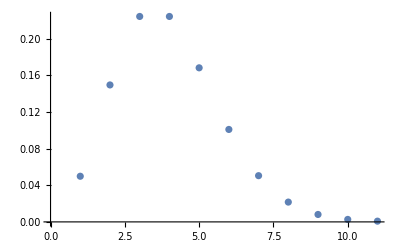

```mathematica
dist=PDF[PoissonDistribution[3],x]
ListPlot[Table[dist,{x,0,10}]]
```

(ⅇ^(-x^2/2))/(√(2 π))

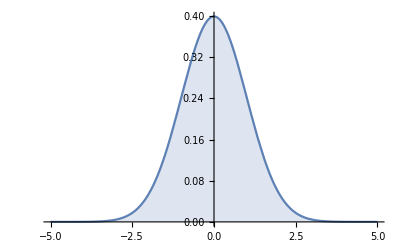

```mathematica
PDF[NormalDistribution[0,1],x]
Plot[%,{x,-5,5},Filling->Axis]
```

```mathematica
PDF[BinormalDistribution[{1,2},{1,1},1/3],{x,y}]
Plot3D[%,{x,-2,4},{y,-1,5}]
```

(3 ⅇ^(-9/16 ((-1+x)^2-2/3 (-1+x) (-2+y)+(-2+y)^2)))/(4 √2 π)

-Graphics3D-

CDF[dist, x] 给出在 x 上计算的分布 dist 的累积分布函数.

CDF[dist, {x1, x2, …}] 给出在 {x1, x2, …} 上计算的分布dist的多变量累积分布函数.

例题：正态分布概率的计算，X服从N (0.5, 2), 计算   P (X < 2), P(|X|> 1.3).

```mathematica
CDF[NormalDistribution[0.5,2],2]
```

0.773373

```mathematica
1-CDF[NormalDistribution[0.5,2],1.3]+CDF[NormalDistribution[0.5,2],-1.3]
```

0.528638

### 6.2 随机变量的各阶矩

Expectation[expr, x \[Distributed] dist] 假定 x 服从概率分布 dist，给出 expr 的期望值.

Expectation[expr, x \[Distributed] data] 假定 x 服从由 data 给定的概率分布，给出 expr 的期望值.

Expectation[expr, {x1, x2, …} \[Distributed] dist] 假定 {x1, x2, …} 服从多元分布 dist，给出 expr 的期望值.

Expectation[expr, {x1 \[Distributed] dist1, x2 \[Distributed] dist2, …}]
假定 x1、x2、… 独立且服从分布 dist1、dist2、…，给出 expr 的期望值.

Expectation[expr\[Distributed] pred, …] 已知 pred，给出 expr 的条件期望值.

```mathematica
Expectation[x^2+7 x+8,x\[Distributed]PoissonDistribution[μ]]
```

8+8 μ+μ^2

```mathematica
Expectation[x^3+4 y-a z,{x,y,z}\[Distributed]MultinomialDistribution[10,{1/2,1/3,1/6}]]
```

-5/6 (-211+2 a)

```mathematica
Expectation[Abs[2 x-1],x\[Distributed]ExponentialDistribution[λ]]
```

(ⅇ^(-λ/2) (4-2 ⅇ^(λ/2)+ⅇ^(λ/2) λ))/λ

```mathematica
Expectation[x^2+1\[Conditioned]x>1/2,x\[Distributed]LaplaceDistribution[0,1/2]]
```

9/4

Variance[list] 给出 list 中元素的样本方差.

Variance[dist] 给出 dist 分布的方差.

```mathematica
Variance[ExponentialDistribution[λ]]
```

1/λ^2

Correlation[dist] 给出多变量符号分布 dist 的相关矩阵.

```mathematica
Correlation[MultivariatePoissonDistribution[μ,{2,3}]]//MatrixForm
```

(1 | μ/(√(2+μ) √(3+μ))
μ/(√(2+μ) √(3+μ)) | 1)

MomentGeneratingFunction[dist, t] 给出分布 dist 的矩母函数，函数的自变量为 t.

MomentGeneratingFunction[dist, {t1, t2, …}] 给出多元分布 dist 的矩母函数

```mathematica
MomentGeneratingFunction[PoissonDistribution[μ],t]
```

ⅇ^((-1+ⅇ^t) μ)

```mathematica
MomentGeneratingFunction[NormalDistribution[μ,σ],t]
```

ⅇ^(t μ+(t^2 σ^2)/2)

```mathematica
MomentGeneratingFunction[BinormalDistribution[ρ],{t1,t2}]
```

ⅇ^(t1^2/2+t2^2/2+t1 t2 ρ)

## 5.2 数理统计

### 1. 样本数据统计（对样本数据处理以及统计）

Length[data] 样本数据个数

Max[data], Min[data] 数据的最大值，最小值

Mean[data] 计算样本数据 data 的均值

Median[data] 计算数据data的中值

Variance[data] 计算样本数据 data 的方差

StandardDeviation[data] 计算样本数据 data 的标准差

CentralMoment[data, k] 计算数据的 k 阶中心矩

Covariance[x, y] 计算x, y 的协方差 (无偏估计）

Correlation[x, y] 计算x, y的相关系数

Count[data, pattern] 计数与pattern匹配的元素个数

BinCounts[list，bins] 计数属于每个区间段的元素个数

BinLists[list, bins] 按照区间段将元素分组

BarChart[{y1, y2, …}] 绘制高度为y1, y2, …的条形图

Histogram[list] 绘直方图

例题：从某厂生产的某种零件中随机抽取120个，测得其质量 （单位 : g） 如下.列出分组表，并作频率直方图.
200 202 203 208 216 206 222 213 209 219 216 203
197 208 206 209 206 208 202 203 206 213 218 207
208 202 194 203 213 211 193 213 208 208 204 206
204 206 208 209 213 203 206 207 196 201 208 207
213 208 210 208 211 211 214 220 211 203 216 221
211 209 218 214 219 211 208 221 211 218 218 190
219 211 208 199 214 207 207 214 206 211 214 201
212 213 211 212 216 206 210 216 204 221 208 209
214 214 199 204 211 201 216 211 209 208 209 202
211 207 220 205 206 216 213 206 206 207 200 198

```mathematica
list={200,202,203,208,216,206,222,213,209,219,216,203,197,208,206,209,206,208,202,203,206,213,218,207,208,202,194,203,213,211,193,213,208,208,204,206,204,206,208,209,213,203,206,207,196,201,208,207,213,208,210,208,211,211,214,220,211,203,216,221,211,209,218,214,219,211,208,221,211,218,218,190,219,211,208,199,214,207,207,214,206,211,214,201,212,213,211,212,216,206,210,216,204,221,208,209,214,214,199,204,211,201,216,211,209,208,209,202,211,207,220,205,206,216,213,206,206,207,200,198};
```

```mathematica
Min[list]
Max[list]
```

190

222

```mathematica
Median[list]
```

208

```mathematica
{Mean[list],StandardDeviation[list]}//N
```

{208.892,6.27894}

```mathematica
count=BinCounts[list,{190,222,4}]
```

{2,3,8,15,40,25,14,12}

```mathematica
center=Table[190+j*4-2,{j,1,8}]
```

{192,196,200,204,208,212,216,220}

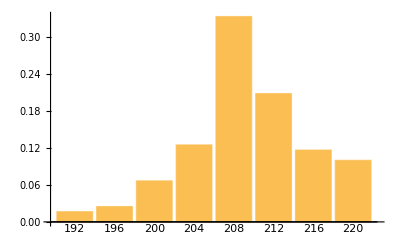

```mathematica
BarChart[count/Length[list],ChartLabels->center]
```

### 2. 参数估计和检验

(1)假设样本服从N[μ, σ^2]分布，求置信度为0.95的置信区间.

```mathematica
Needs["HypothesisTesting`"]
MeanCI[list]
MeanCI[list,ConfidenceLevel->0.90]
```

{207.757,210.027}

{207.941,209.842}

VariarIceCI[list], 由数据 list 求总体方差的置信区间

FindDistributionParameters[data, dist] 
假设数据服从某类型的分布时，估计分布的参数.

ParameterEstimator是FindDistributionParameters 的一个选项，指定要使用什么参数估计方法.项缺省时是指在dist分布的假定下，获得极大似然参数估计量，下列基本设置可用在 ParameterEstimator 上：

"MaximumLikelihood" 使对数似然函数最大化
"MethodOfMoments" 匹配原始矩
"MethodOfCentralMoments" 匹配中心矩
"MethodOfCumulants" 匹配累积量
"MethodOfFactorialMoments" 匹配阶乘矩

```mathematica
data=RandomVariate[ExponentialDistribution[2],100]
```

{0.69516,0.183292,1.54831,0.446877,0.252931,2.12011,0.459164,1.70466,0.655983,0.0130631,0.28753,0.608063,0.197721,0.752599,0.259707,0.57035,0.990868,0.122114,0.986794,1.22948,0.313212,0.130497,0.165277,0.127539,0.0507956,1.03427,0.194459,3.43556,0.303204,1.21061,0.310545,0.105053,0.10038,1.23467,1.06416,0.591486,0.334277,0.344473,0.989604,0.358269,0.62812,0.755528,0.448743,0.253581,0.771929,0.792084,0.0105705,0.123944,0.958213,0.376303,0.673207,2.22023,0.22303,0.751918,0.490336,0.922177,0.105682,0.326182,0.0551502,0.0490806,1.49426,0.136896,0.114857,0.18904,0.223032,2.03206,0.279486,0.273269,1.42516,1.66804,0.49721,0.186202,0.411396,0.577897,0.74512,0.331497,0.625399,0.254253,0.116342,0.308348,0.622796,0.17503,0.657375,0.63998,0.299391,0.182505,0.0969411,0.497777,1.0425,0.297246,0.480042,0.12531,0.115165,0.217829,1.13106,0.0426882,0.679649,0.499136,0.271446,0.70041}

```mathematica
FindDistributionParameters[data,ExponentialDistribution[lambda]]
```

{lambda→1.72167}

```mathematica
Mean[data]
```

0.580832

```mathematica
FindDistributionParameters[data,ExponentialDistribution[lambda],
ParameterEstimator->"MethodOfMoments"]
```

{lambda→1.72167}

### 3. 回归分析（用函数拟合数据）

```mathematica
(1)线性回归模拟
```

LinearModelFit[data, funs, vars]
由 data 的数据求由基函数表 funs 中的函数的线性组合构成的回归方程，

其中 data的一般形式是 {{x11，x12，…, y1}, {x12, x22, …, y2}, …}, funs 的一般形式为 {f1, f2, …}, vars的一般形式 {x1, x2, …}, 它是 funs 中函数的自变量表.

例题：为研究某一化学反应过程中温度 x 对产品质量y 的影响，测得数据见表

x | 100 | 110 | 120 | 130 | 140 | 150 | 160 | 170 | 180 | 190
y | 45 | 51 | 54 | 61 | 66 | 70 | 74 | 78 | 85 | 89
求 : y 关于x的线性回归方程，并分析回归效果的显著性.

```mathematica
data={{100,45},{110,51},{120,54},{130,61},{140,66},{150,70},{160,74},{170,78},{180,85},{190,89}};
LinearModelFit[data,{1,x},{x}]
```

FittedModel[-2.73939+0.48303 x]

例题：一项关于水稻亩产量的研究中从 10 个农场获得水稻亩产量y与施肥量x1 播种量x2的数据，
x1 38 39 40 41 42 43 44 45 46 47
x2 50 50 52 56 60 64 60 61 62 63
y   50 51 55 59 62 64 66 68 69 71
试写出回归方程.

```mathematica
data={{38,50,50},{39,50,51},{40,52,55},{41,56,59},{42,60,62},{43,64,64},{44,58,66},{46,63,68},{47,62,69},{48,61,71}};
LinearModelFit[data,{1,x,y},{x,y}]
```

FittedModel[-30.5772+1.55424 x+0.443674 y]

#### (2) 非线性回归模拟

NonlinearModelFit[{{x11, x12, …, y1}, {x21, x22, …, y2}, …}, form, {β1, …}, {x1, …}]
按form给出的函数拟合所给出的数据，βi是参数表，xi是变量表.

```mathematica
data={{0,1},{1,0},{3,2},{5,4},{6,4},{7,5}};
nlm=NonlinearModelFit[data,Log[a+b x^2],{a,b},x]
```

FittedModel[Log[1.50632+1.42633 x^2]]